# Notebook for “A mathematical model of gossip, reputations, and cooperation” Authors: Mari Kawakatsu*, Taylor Kessinger*, Joshua Plotkin Description: Notebook for generating all figures in the main text and the SI

## Part 0: Plot settings

```mathematica
ClearAll["Global`*"]

(* define plot theme *)
Themes`AddThemeRules["mk_plot"
,LabelStyle->14
,Frame->{{True,False},{True,False}}
,FrameStyle->Black
,PlotRangePadding->Scaled[0.02]
,TicksStyle->12
];

Themes`AddThemeRules["mk_densityplot"
,ContourPlot
,LabelStyle->14
,Frame->{{True,False},{True,False}}
,FrameStyle->Black
,AspectRatio->1
,GridLines->None
,PlotRangePadding->Scaled[.02]
,InterpolationOrder->0
,ColorFunction->(ColorData[{"SunsetColors","Reverse"}][Rescale[#,{1,0},{1.,0.0}]]&)
,ColorFunctionScaling->False
,Contours->9
,TicksStyle->12
,Method->{"TransparentPolygonMesh"->True}
];

(* define axis labels *)
MakeLabel[name_?StringQ,sym_?StringQ,boost_:1,size_:14]:=Row[{
Style[name<>" (",FontFamily->"Arial",FontSize->size]
,Style[sym,FontFamily->"Times New Roman",FontSize->size+boost]
,Style[")",FontFamily->"Arial",FontSize->size]
},BaselinePosition->Bottom];

τlabel=MakeLabel["Gossip duration","τ",2];
τstarlabel=MakeLabel["Critical gossip duration","τ^*",2];
τstarALLDlabel=MakeLabel["Critical gossip duration","(τ^*)_ALLD",2];
Qlabel=MakeLabel["Gossip probability","Q",1];
bclabel=MakeLabel["Benefit-to-cost ratio","b/c",1];
tlabel=MakeLabel["Time","t",1];
replabel=MakeLabel["Averate reputation","r̃",1];
agreelabel=MakeLabel["Agreement level","(g̃)_2+(b̃)_2",1];
uelabel=MakeLabel["Execution error rate","u_e",2];
ualabel=MakeLabel["Assessment error rate","u_a",2];
betalabel=MakeLabel["Gossip bias","β",1];

(* define legend elements *)
MakeLegendElement[sym_?StringQ,value_,size_:12,numform_:{2,1},baseline_:0]:=(
If[value==Infinity
,Row[{Style["  "<>sym,FontFamily->"Times New Roman",FontSize->size]
,Style[" → ",FontFamily->"Times New Roman",FontSize->size],Style["∞",FontFamily->"Arial",FontSize->size+1]}
,BaselinePosition->Scaled[baseline]]
,Row[{Style["  "<>sym,FontFamily->"Times New Roman",FontSize->size]
,Style[" = ",FontFamily->"Arial",FontSize->size],Style[NumberForm[value,numform],FontFamily->"Arial",FontSize->size-1]}
,BaselinePosition->Scaled[baseline]]
]
)

MakeLegendElement2[sym_?StringQ,value_?StringQ,size_:12]:=Row[{
Style["  "<>sym,FontFamily->"Times New Roman",FontSize->size]
,Style[" = ",FontFamily->"Arial",FontSize->size]
,Style[value,FontFamily->"Arial",FontSize->size-1]}
,BaselinePosition->Scaled[0.0]]

(* define frame ticks *)
MakeFrameTicks[xdigits_:2,ydigits_:2,xmax_:1.,ymax_:1.2,xmin_:0,ymin_:0,xticknum_:4,yticknum_:4]:=Module[{yticks,xticks},
xticks=(({#,NumberForm[#,{xdigits,xdigits-1}],{0,0.02}})&/@Subdivide[xmin,xmax,xticknum]);
yticks=(({#,NumberForm[#,{ydigits,ydigits-1}],{0,0.02}})&/@Subdivide[ymin,ymax,yticknum]);
{{yticks,None},{xticks,None}}
]

(* custom colors *)
orange1=RGBColor["#fdbf6f"];
orange2=RGBColor["#ec7014"];
orange3=RGBColor["#cc4c02"];
orange4=RGBColor["#993404"];
orange5=RGBColor["#662506"];
ylorrd1=RGBColor["#fec44f"];
ylorrd2=RGBColor["#fe9929"];
ylorrd3=orange2;
ylorrd4=RGBColor["#cc4c02"];
ylorrd5=RGBColor["#993404"];
inferno1=RGBColor["#f4df53"];(* colors based on the inferno color palette *)
inferno2=RGBColor["#fbb61a"];
inferno3=orange2;
inferno4=RGBColor["#bc3754"];
inferno5=RGBColor["#781C6D"];
inferno6=RGBColor["#320a5e"];
lightgray=GrayLevel[0.5];
blue1=RGBColor["#a6cee3"];
blue2=RGBColor["#5ca3cc"];
blue3=RGBColor["#1f78b4"];
olive1=RGBColor["#d6ebad"];
olive2=RGBColor["#a4d246"];
olive3=RGBColor["#5c7b1e"];
green1=RGBColor["#b2df8a"];
green2=RGBColor["#72c056"];
green3=RGBColor["#33a02c"];
slateblue1=RGBColor["#d2cdf0"];
slateblue2=RGBColor["#968bdc"];
slateblue3=RGBColor["#5f51b8"];
purple1=RGBColor["#cab2d6"];
purple2=RGBColor["#9b71b8"];
purple3=RGBColor["#6a3d9a"];

olives={olive3,olive2,olive1};
blues={blue3,blue2,blue1};
greens={green3,green2,green1};
slateblues={slateblue3,slateblue2,slateblue1};
purples={purple3,purple2,purple1};

(* for simplex plots *)
TernCoords[x_,y_]:={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};

(* custom export *)
(*NotebookDirectory[];*)
savefig[filename_,plot_]:=Module[{directory},
directory=NotebookDirectory[]<>"/plots/";
Export[directory<>filename,plot,"AllowRasterization"->False];
Print["Exported "<>filename<>" to ./plots/"]
]
```

## Part 1: Mapping between the two gossip processes (Fig S1)

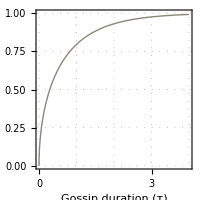

Exported FigS1.pdf to ./plots/

```mathematica
(* define functions *)
Qfromτ[τ_]:=Sqrt[1-Exp[-τ]];
τfromQ[Q_]:=-Log[1-Q^2];

(* plot *)
Clear[τmax,uaa,uee];τmax =4; uaa=0.02;uee=0.02;
pS1=Plot[
Evaluate[Qfromτ[τ]],{τ,0,τmax}
,PlotRange->{{0,τmax},{0,1}}
,PlotStyle->{Thick,RGBColor["#8b8878"]}
,FrameTicks->MakeFrameTicks[1,3,τmax,1.] (* num digits for x axis = 1, for y axis = 3 *)
,FrameLabel->{τlabel,Qlabel}
,PlotTheme->"mk_plot"
,ImageSize->{200,200}
,AspectRatio->1
,GridLines->Automatic
,GridLinesStyle->Directive[Dotted, Gray]
]

(* export *)
savefig["FigS1.pdf",pS1]
```

## Part 2: Dynamics of strategy competition with noiseless gossip (Figs 2A–D)

## 2.1: Replicator dynamics (Figs 2A,C)

### Functions

```mathematica
setupternaryequations[p_?NumericQ,q_?NumericQ,ua_?NumericQ,ue_?NumericQ,τ_?NumericQ]:=(
Clear[eps,pgc,pbc,pgd,pbd,r,g2,b2,d2,g2gossip,b2gossip,d2gossip,drx,dry,drz];
Clear[fx,fy,fz];

(* observer view - donor intent - probgood *)
eps:=(1-ua)(1-ue)+ua*ue;
pgc=eps;
pbc=p(eps-ua)+q(1-eps-ua)+ua;
pgd=ua;
pbd=q(1-2ua)+ua;

(* generation equations for reputation relations *)
r:=fx rx+fy ry+fz rz;
g2:=fx*rx^2+fy*ry^2 +(1-fx-fy)*rz^2;
b2:=fx*(1-rx)^2+fy*(1-ry)^2 +(1-fx-fy)*(1-rz)^2;
d2:=fx*(1-rx)*rx+fy*(1-ry)*ry+(1-fx-fy)*(1-rz)*rz;

(* gossip  *)
g2gossip:=g2+d2(1-Exp[-τ]);
b2gossip:=b2+d2(1-Exp[-τ]);
d2gossip:=d2*Exp[-τ];

(* reputation dynamics *)
drx=FullSimplify[r*pgc+(1-r)*pbc];
dry=FullSimplify[r*pgd+(1-r)*pbd];
drz=FullSimplify[g2gossip*pgc+d2gossip*(pbc+pgd)+b2gossip*pbd];
)

nsoln[uaa_?NumericQ,uee_?NumericQ,δδ_?NumericQ,ττ_?NumericQ,fxX_?NumericQ,fyY_?NumericQ,fzZ_?NumericQ]:=Module[{},
(* solve for equilibrium reputations numerically *)
FindRoot[{
rx==drx(*r*pgc+(1-r)*pbc*),
ry==dry(*r*pgd+(1-r)*pbd*),
rz==drz(*g2gossip*pgc+d2gossip*(pbc+pgd)+b2gossip*pbd*)
}/.{ua->uaa, ue->uee,δ->δδ,τ->ττ,fx->fxX,fy->fyY,fz->fzZ}
,{{rx,.35},{ry,.4},{rz,.45}}
]
];

fsoln[fx_, fy_,b_,c_,ua_,ue_,δ_,τ_] :=Module[
{fz,repsoln,f1X,f1Y,f1Z,f2X,f2Y,f2Z,pi1X,pi2X,pi1Y,pi2Y,pi1Z,pi2Z,pi,pix,piy,piz,fxdot,fydot,fzdot}, 

Clear[fz,repsoln,pi,pix,piy,piz,fxdot,fydot,fzdot];
fz = 1 - fx - fy;
repsoln = nsoln[ua,ue,δ,τ,fx,fy, fz];

pix=(1-ue)(b (fx+fz*rx) - c)/.repsoln;
piy=(1-ue)(b (fx+fz*ry))/.repsoln;
piz=(1-ue)(b (fx+fz*rz)- c*(fx rx+fy ry+fz rz))/.repsoln;
pi=fx pix+fy piy+fz piz;

fxdot =fx (pix-pi);
fydot =fy (piy-pi);
fzdot =fz (piz-pi);

{fxdot, fydot, fzdot}
]

MakeTernaryPlot[b_,c_,ua_,ue_,δ_,τ_,p_,q_] :=Module[{diskradius,fvals,dotfx,dotfy,dotfz,vX,vY,textoffset,thickness,vlabels,streampoints,dp,error,xf,ternplot,plot,eqpoints} ,
(*MakeTernaryPlot[b,c,ua,ue,δ,τ,p,q] *)

setupternaryequations[p,q,ua,ue,τ];
(*Print[drx];*)

fvals[fx_,fy_] := fsoln[fx,fy,b,c,ua,ue,δ,τ];

dotfx[fx_?NumericQ,fy_?NumericQ]:=fvals[fx,fy][[1]];
dotfy[fx_?NumericQ,fy_?NumericQ]:=fvals[fx,fy][[2]];
dotfz[fx_?NumericQ,fy_?NumericQ]:=fvals[fx,fy][[3]];

vX:=dotfx[fx,fy];
vY:=dotfy[fx,fy];

(* plot settings *)
diskradius=.015;
textoffset=.075;
thickness=.005;

vlabels={
Graphics[Text[Style["ALLD",16],{-textoffset*0.5,-textoffset}]]
,Graphics[Text[Style["ALLC",16],{1+textoffset*0.5,-textoffset}]]
,Graphics[Text[Style["DISC",16],{1/2,Tan[Pi/3]/2+textoffset}]]
(*,Graphics[Text[Style[("τ = "<>ToString[NumberForm[τ,{2,2}]]),16],{1/2,Tan[Pi/3]/2+textoffset*3}]]*)
};
streampoints=DeleteCases[Flatten[Table[If[0≤fx0+fy0≤1,{fx0,fy0},{}],{fx0,Subdivide[1.,20][[;;]]},{fy0,Subdivide[1.,20][[;;]]}],1],{}];

(* equilibrium markers *) 
stablept[loc_]:={blue3,EdgeForm[Directive[blue3,Thickness[0.01]]],Disk[loc,0.0225]};
unstablept[loc_]:={White,EdgeForm[Directive[blue3,Thickness[0.01]]],Disk[loc,0.0225]};

(* these are set up manually for cases with τ = 0 and 0.4 with the parameters used in Fig 2. *)
(* for all other parameter combos, a filled circle will appear at the ALLD vertex and an empty circle at the ALLC vertex *) 
If[b==5&&c==1&&ua==0.02&&ue==0.02&&δ==1&&p==0&&q==1&&(τ==0.0||τ==0.4),
If[τ==0.0,eqpoints={stablept[{0,0}],unstablept[{1,0}],unstablept[{1/2,Sqrt[3]/2}]},
If[τ==0.4,eqpoints={stablept[{0,0}],unstablept[{1,0}],stablept[{1/2,Sqrt[3]/2}],unstablept[TernCoords[fx,fy]/.FindRoot[{vX==0,vY==0},{{fx,0.,0.,0.02},{fy,0.5,0.,1.}}]]}
,(* else just a point at the ALLD vertex *)eqpoints={stablept[{0,0}],unstablept[{1,0}]}
]]
,eqpoints={stablept[{0,0}]}
];

(* plot *) 
dp=StreamPlot[{vX,vY},{fx,0,1},{fy,0,1}
,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None, RegionBoundaryStyle->Directive[Thin,Black],Evaluated -> True
,StreamPoints->streampoints(*Fine*)
,StreamScale->{Large,All,0.0225}
,StreamColorFunction->None
,StreamStyle->lightgray
];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];

plot=Show[{ternplot,vlabels},Epilog->eqpoints,ImageSize->{240,240},PlotRangePadding->.05];

(* show plot *)
Return[plot]
]
```

### Fig 2A

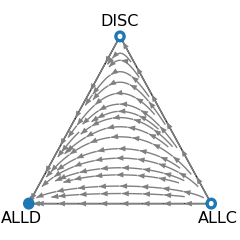

Exported Fig2A.pdf to ./plots/

```mathematica
Clear[params];params={b->5,c->1,δ->1,τ->0.0,ua->0.02,ue->0.02,rx0->0.35,ry0->0.4,rz0->0.45,p->0,q->1};
p2A=MakeTernaryPlot[ Sequence @@ ({b,c,ua,ue,δ,τ,p,q}/.params) ]

savefig["Fig2A.pdf",p2A]
```

### Fig 2C

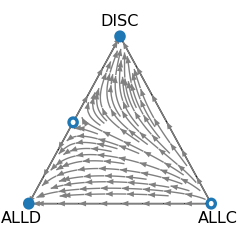

Exported Fig2C.pdf to ./plots/

```mathematica
Clear[params];params={b->5,c->1,δ->1,τ->0.4,ua->0.02,ue->0.02,rx0->0.35,ry0->0.4,rz0->0.45,p->0,q->1};
p2C=MakeTernaryPlot[ Sequence @@ ({b,c,ua,ue,δ,τ,p,q}/.params) ]

savefig["Fig2C.pdf",p2C]
```

## 2.2: Stochastic simulations (Figs 2B,D)

### Functions

```mathematica
Clear[trajN,τMoran];

MakeSimPlot[τMoran_,trajN_:100]:=Module[{filePattern,fileNames,dataList,transformedDataList,xData,yData,transformedData,LastElements,textoffset,vlabels,colors,plots,points,simplex,simPlot},

(* import simulation data *)
filePattern=NotebookDirectory[]<>"simdata/*_tau_"<>ToString[NumberForm[τMoran,{Infinity,1}]]<>"_N_"<>ToString[trajN]<>"_*.csv";fileNames=FileNames[filePattern];dataList=Import[#]&/@fileNames;

(* format data *)
transformedDataList={};
Do[
xData=Data[[1,1;; ;;30]];
yData=Data[[2,1;; ;;30]];
transformedData=TernCoords@@@Transpose[{xData,yData}/trajN];
AppendTo[transformedDataList,transformedData],{Data,dataList}
];
LastElements=Last/@Transpose /@ dataList;

(* plot settings *)
textoffset=.075;
vlabels={
Graphics[Text[Style["ALLD",16],{-textoffset*0.5,-textoffset}]]
,Graphics[Text[Style["ALLC",16],{1+textoffset*0.5,-textoffset}]]
,Graphics[Text[Style["DISC",16],{1/2,Tan[Pi/3]/2+textoffset}]]
};
colors=If[τMoran==0.0,ConstantArray[lightgray,6],If[τMoran==0.2,Flatten[{ConstantArray[#,3]&/@{lightgray,blue3}}],ConstantArray[Red,6]]];

(* plot elements *)
plots=MapThread[ListLinePlot[{#1},PlotStyle->{Directive[Opacity[0.7],Thickness[0.006],#2]}]&,{transformedDataList,colors}];
(*points=MapThread[{PointSize[0.03],#2,Point[#1]} &,{transformedDataList[[All,1]],colors}];*)
points=MapThread[{Style[Text["×",#1],#2,FontSize->24]} &,{transformedDataList[[All,1]],colors}];
simplex=Graphics[{EdgeForm[{Thin,Black}],FaceForm[None],Polygon[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]}];

(* show plot *)
simPlot=Show[{vlabels,simplex,plots},Epilog->{points},ImageSize->{240,240},PlotRangePadding->.05];

Return[simPlot]
]
```

### Fig 2B

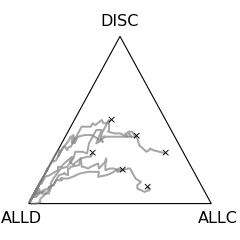

Exported Fig2B.pdf to ./plots/

```mathematica
Clear[trajN,τMoran];trajN=100;τMoran=0.0;
p2B=MakeSimPlot[τMoran,trajN]

savefig["Fig2B.pdf",p2B]
```

### Fig 2D

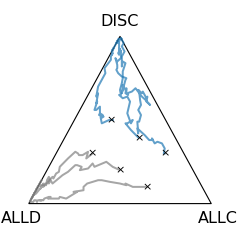

Exported Fig2D.pdf to ./plots/

```mathematica
Clear[trajN,τMoran];trajN=100;τMoran=0.2;
p2D=MakeSimPlot[τMoran,trajN]

savefig["Fig2D.pdf",p2D]
```

## Part 3: Stability analysis with noiseless gossip (Figs 2E–G, S2, S3, and S7)

## 3.1: Stability of the DISC equilibrium under Stern Judging (Figure 2E)

### Functions

```mathematica
Clear[bcstar,eτstar,τstar,τstarplot];
bcstar[ua_,ue_]:=(1/((1-2 ua) (1-ue)));
eτstar[b_,c_,ua_,ue_]:=2*(1-1/2*(b/c)/((b/c)-1/(2(1-ua))))((b/c)/((b/c)-1/((1-2 ua) (1-ue))));
τstar[b_,c_,ua_,ue_]:=Log[eτstar[b,c,ua,ue]];
τstarplot[b_,c_,ua_,ue_]:=If[(b/c>bcstar[ua,ue])&&(eτstar[b,c,ua,ue]>0),Log[eτstar[b,c,ua,ue]],If[b/c>bcstar[ua,ue],Log[eτstar[b,c,ua,ue]],Undefined]];

Clear[ua,ue,bmax,τmax,c];
MakeStabilityPlot[ua_:0.02,ue_:0.02,bmax_:7,τmax_:1.2,c_:1]:=Plot[
Evaluate[τstarplot[b,c,ua,ue]],{b,1,bmax}
,Filling->Top
,FillingStyle->{Opacity[0.15],orange1}
,PlotRange->{{1,bmax},{-0.01,τmax+0.01}}
,PlotStyle->{Thick,orange2}
,FrameTicks->MakeFrameTicks[1,2,bmax,τmax,1,0,3,3]
,FrameLabel->{bclabel,τstarlabel}
,PlotTheme->"mk_plot"
,ImageSize->{220,220}
,AspectRatio->1
,Epilog->{
Dashed,Gray,Line[{{bcstar[ua,ue],-0.5},{bcstar[ua,ue],τmax+0.005}}]
,Text[Style["DISC stable",orange2,FontSize->14],{6.75,1.15},{1,1}]
,Text[Style[MakeLegendElement["b/c",Round[bcstar[ua,ue],10.^-3],10.5,{4,3}],Gray],{bcstar[ua,ue]+0.2,0.01},{-0.8,0.35},{0,0.95}]
,Black,PointSize[0.03],Point[{5,0.0}]
,Black,PointSize[0.03],Point[{5,0.4}]
}
]
```

### Fig 2E

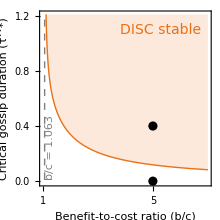

Exported Fig2E.pdf to ./plots/

```mathematica
Clear[bmax,cc,uaa,uee,τmax];bmax =7;cc=1;uaa=0.02;uee=0.02;τmax=1.2;
p2E=MakeStabilityPlot[uaa,uee,bmax,τmax,cc]

savefig["Fig2E.pdf",p2E]
```

## 3.2: Stability of the DISC equilibrium against ALLD under any norm (p, q) (Fig S3)

### Functions

```mathematica
Clear[bcstar,eτALLDstar,τALLDstar,τALLDstarplot];

bcstar[ua_,ue_]:=(1/((1-2 ua) (1-ue))); (*same as before*)
eτALLDstar[b_,c_,ua_,ue_,p_,q_]:=(1-p+q)(1-((ua+q (1-2 ua))/(1+q (1-2 ua)))(b/c)/((b/c)-1/(1+q (1-2 ua))))((b/c)/((b/c)-1/((1-2 ua) (1-ue))));
τALLDstar[b_,c_,ua_,ue_,p_,q_]:=Log[eτALLDstar[b,c,ua,ue,p,q]];
τALLDstarplot[b_,c_,ua_,ue_,p_,q_]:=If[(b/c>bcstar[ua,ue])&&(eτALLDstar[b,c,ua,ue,p,q]>1),Log[eτALLDstar[b,c,ua,ue,p,q]],If[(b/c>bcstar[ua,ue]),Log[eτALLDstar[b,c,ua,ue,p,q]],Undefined]];
```

```mathematica
bmax =7; uaa=0.02;uee=0.02;τmax=1.2;

pS3A=Plot[
{Evaluate[τALLDstarplot[b,c,ua,ue,p,q]/.{c->1,ua->uaa,ue->uee,p->1,q->1}](*SS*)
,Evaluate[τALLDstarplot[b,c,ua,ue,p,q]/.{c->1,ua->uaa,ue->uee,p->0,q->1}](*SJ*)
,Evaluate[τALLDstarplot[b,c,ua,ue,p,q]/.{c->1,ua->uaa,ue->uee,p->0,q->0}](*SH*)
},{b,1,bmax}
,Filling->None
,FillingStyle->Opacity[0.05]
,PlotRange->{{0.99,bmax},{0,τmax}}
,PlotStyle->(Directive[Thick,#]&/@{ylorrd5,ylorrd3,ylorrd1})
,PlotLegends->Placed[LineLegend[Automatic,Style[#,12]&/@{" Simple Standing"," Stern Judging"," Shunning"},Spacings->0.15,LegendLayout->"ReversedColumn"],{0.65,0.5}]
,FrameTicks->MakeFrameTicks[1,2,bmax,τmax,1,0,3,3]
,FrameLabel->{bclabel,τstarALLDlabel}
,PlotTheme->"mk_plot"
,ImageSize->{240,240}
,AspectRatio->1
,Epilog->{Dashed,Gray,Line[{{bcstar[uaa,uee],-10},{bcstar[uaa,uee],τmax+.005}}]
}
];

ps={0,0.5,1};pslabeled={"0 (SJ)","0.5","1 (SS)"};qq=1;
pS3B=Plot[
Evaluate[
Evaluate[τALLDstarplot[b,c,ua,ue,p,q]/.{c->1,ua->uaa,ue->uee,p->#,q->qq}]&/@ps
]
,{b,1,bmax}
,PlotRange->{{0.99,bmax},{0,τmax}}
,PlotStyle->(Directive[Thick,#]&/@{ylorrd3,ylorrd4,ylorrd5})
(*,PlotLegends->Placed[
LineLegend[Automatic,Style["p = "<>ToString[#]<>If[#==0," (SJ)",If[#==1," (SS)",""]],12]&/@ps,Spacings->0.15],
{0.75,0.5}]*)
,PlotLegends->Placed[
LineLegend[Automatic,MakeLegendElement2["p",#,13]&/@pslabeled,Spacings->-0.075,LegendLayout->"ReversedColumn"],
{0.75,0.5}]
,FrameTicks->MakeFrameTicks[1,2,bmax,τmax,1,0,3,3]
,FrameLabel->{bclabel,τstarALLDlabel}
,PlotTheme->"mk_plot"
,ImageSize->{240,240}
,AspectRatio->1
,Epilog->{Dashed,Gray,Line[{{bcstar[uaa,uee],-10},{bcstar[uaa,uee],τmax+.005}}]
,Text[Style[MakeLegendElement["q",qq,13,{2,2}],Gray],{7,1.2},{1,1}]
}
];

qs={1,0.5,0};pp=0;
qslabeled={"1 (SJ)","0.5","0 (SH)"};

pS3C=Plot[
Evaluate[
Evaluate[τALLDstarplot[b,c,ua,ue,p,q]/.{c->1,ua->uaa,ue->uee,p->pp,q->#}]&/@qs
]
,{b,1,bmax}
,PlotRange->{{0.99,bmax},{0,τmax}}
,PlotStyle->(Directive[Thick,#]&/@{ylorrd3,ylorrd2,ylorrd1})
,PlotLegends->Placed[
LineLegend[Automatic,MakeLegendElement2["q",#,13]&/@qslabeled,Spacings->-0.075,LegendLayout->"ReversedColumn"],
{0.75,0.5}]
,FrameTicks->MakeFrameTicks[1,2,bmax,τmax,1,0,3,3]
,FrameLabel->{bclabel,τstarALLDlabel}
,PlotTheme->"mk_plot"
,ImageSize->{240,240}
,AspectRatio->1
,Epilog->{Dashed,Gray,Line[{{bcstar[uaa,uee],-10},{bcstar[uaa,uee],τmax+.005}}]
,Text[Style[MakeLegendElement["p",pp,13,{2,2}],Gray],{7,1.2},{1,1}]
}
];

pp=0.75;
pS3D=Plot[
Evaluate[
Evaluate[τALLDstarplot[b,c,ua,ue,p,q]/.{c->1,ua->uaa,ue->uee,p->pp,q->#}]&/@qs
]
,{b,1,bmax}
,PlotRange->{{0.99,bmax},{0,τmax}}
,PlotStyle->(Directive[Thick,#]&/@{ylorrd3,ylorrd2,ylorrd1})
,PlotLegends->Placed[
LineLegend[Automatic,MakeLegendElement["q",#,13,{2,2}]&/@qs,Spacings->-0.075,LegendLayout->"ReversedColumn"],
{0.75,0.5}]
,FrameTicks->MakeFrameTicks[1,2,bmax,τmax,1,0,3,3]
,FrameLabel->{bclabel,τstarALLDlabel}
,PlotTheme->"mk_plot"
,ImageSize->{240,240}
,AspectRatio->1
,Epilog->{Dashed,Gray,Line[{{bcstar[uaa,uee],-10},{bcstar[uaa,uee],τmax+.005}}]
,Text[Style[MakeLegendElement["p",pp,13,{2,2}],Gray],{7,1.2},{1,1}]
}
];
```

### Fig S3

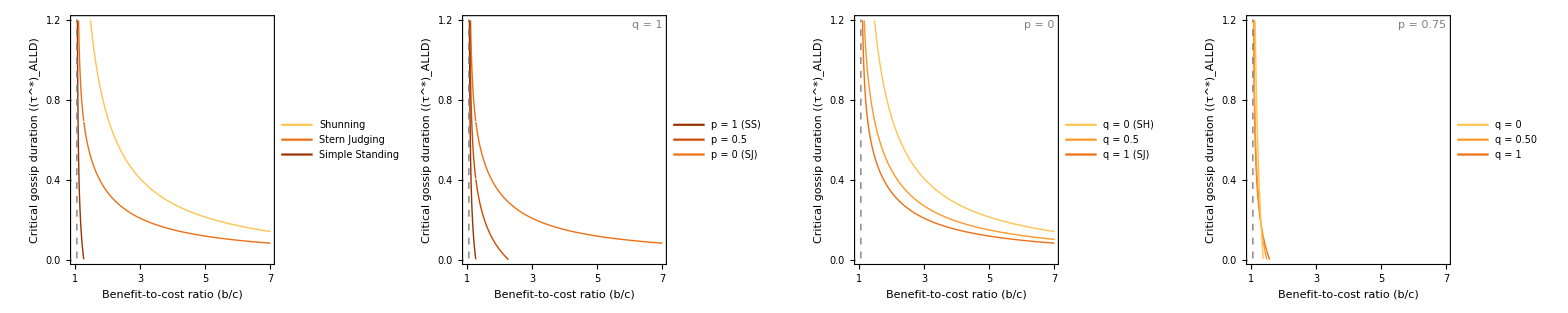

Exported FigS3.pdf to ./plots/

```mathematica
pS3=Grid[{{pS3A,pS3B,pS3C,pS3D}},Spacings->2]

savefig["FigS3.pdf",pS3]
```

## 3.3: Average reputations and agreement levels at the DISC equilibrium under Stern Judging (Figs 2F–G)

### Functions

```mathematica
setuptemporaleqns[p_,q_]:=(
ClearAll[eps,pgc,pbc,pgd,pbd,r,g2,b2,d2,g2gossip,b2gossip,d2gossip,pix,piy,piz,pi];

eps:=(1-ua)(1-ue)+ua*ue;
pgc=eps;
pbc=p(eps-ua)+q(1-eps-ua)+ua;
pgd=ua;
pbd=q(1-2ua)+ua;

r:=(fx[t]*rx[t] + fy[t]*ry[t] + (1-fx[t]-fy[t])*rz[t]);
g2:=(fx[t]*rx[t]^2+fy[t]*ry[t]^2 +(1-fx[t]-fy[t])*rz[t]^2);
b2:=(fx[t]*(1-rx[t])^2+fy[t]*(1-ry[t])^2 +(1-fx[t]-fy[t])*(1-rz[t])^2);
d2:=(fx[t]*(1-rx[t])*rx[t]+fy[t]*(1-ry[t])*ry[t] +(1-fx[t]-fy[t])*(1-rz[t])*rz[t]);

g2gossip:=g2+d2(1-Exp[-τ]);
b2gossip:=b2+d2(1-Exp[-τ]);
d2gossip:=d2*Exp[-τ];

pix:=(1-ue)(b(fx[t]+(1-fx[t]-fy[t])*rx[t])-c);
piy:=(1-ue)(b(fx[t]+(1-fx[t]-fy[t])*ry[t]));
piz:=(1-ue)(b(fx[t]+(1-fx[t]-fy[t])*rz[t])-c*r);
pi:=fx[t]*pix+fy[t]*piy+(1-fx[t]-fy[t])*piz;

eqns:={
fx'[t]==fx[t]*(pix-pi),
fy'[t]==fy[t]*(piy-pi),
rx'[t]==δ(r*pgc+(1-r)*pbc-rx[t]),
ry'[t]==δ(r*pgd+(1-r)*pbd-ry[t]),
rz'[t]==δ((g2gossip*pgc+d2gossip*(pbc+pgd)+b2gossip*pbd)-rz[t]),
fx[0]==fx0,
fy[0]==fy0,
rx[0]==rx0,
ry[0]==ry0,
rz[0]==rz0
}
)

PlotNumerical2[paramset_,τset_,tmax_:100]:=Module[{sol,p1,p2,p3,fxs1,fys1,rxs1,rys1,rzs1,fxs2,fys2,rxs2,rys2,rzs2,fxs3,fys3,rxs3,rys3,rzs3,fxs0,fys0,rxs0,rys0,rzs0,fx0val,fy0val},

setuptemporaleqns[Sequence @@ ({p,q}/.paramset)];

(*only check DISC equilibrium*)
{fxs1,fys1,rxs1,rys1,rzs1}=NDSolveValue[eqns/.paramset/.{τ->τset[[1]]}/.{fx0->0,fy0->0},{fx,fy,rx,ry,rz},{t,0,tmax},Method->Automatic];
{fxs2,fys2,rxs2,rys2,rzs2}=NDSolveValue[eqns/.paramset/.{τ->τset[[2]]}/.{fx0->0,fy0->0},{fx,fy,rx,ry,rz},{t,0,tmax},Method->Automatic];
{fxs3,fys3,rxs3,rys3,rzs3}=NDSolveValue[eqns/.paramset/.{τ->τset[[3]]}/.{fx0->0,fy0->0},{fx,fy,rx,ry,rz},{t,0,tmax},Method->Automatic];

(*compute public case by taking τ to ∞*) 
eqnspublic=eqns;eqnspublic[[5,2]]=Limit[eqnspublic[[5,2]],τ->∞];
{fxs0,fys0,rxs0,rys0,rzs0}=NDSolveValue[eqnspublic/.paramset/.{fx0->0,fy0->0},{fx,fy,rx,ry,rz},{t,0,tmax},Method->Automatic];

p1=Plot[
{rzs0[t],rzs1[t],rzs2[t],rzs3[t]},{t,0,tmax-1}
,PlotStyle->Flatten[{Directive[Dashing[{0.01,0.0075}],Darker@Gray],(Directive[Thick,#]&/@greens)}]
,PlotRange->{Automatic,{0,1}}
,FrameLabel->{None,replabel}
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,1,2]),None},{{{tmax/2,tlabel,{0,0}}},None}}
,ImageSize->{260,175}
,ImagePadding->{{55,10},{25,10}}
,AspectRatio->3/4
,PlotTheme->"mk_plot"
,PlotLegends->Placed[
LineLegend[Automatic,(Style[#,13]&/@Flatten[{MakeLegendElement["τ",Infinity],(MakeLegendElement["τ",#,12]&/@τs)}])
,LegendMarkerSize->16,Spacings->{-0.,-0.4}],{Right,Bottom}]
];
p2=Plot[
{rzs0[t]^2+(1-rzs0[t])^2+2*rzs0[t](1-rzs0[t])*Limit[(1-Exp[-τ]),τ->∞]
,rzs1[t]^2+(1-rzs1[t])^2+2*rzs1[t](1-rzs1[t])*(1-Exp[-τset[[1]]])
,rzs2[t]^2+(1-rzs2[t])^2+2*rzs2[t](1-rzs2[t])*(1-Exp[-τset[[2]]])
,rzs3[t]^2+(1-rzs3[t])^2+2*rzs3[t](1-rzs3[t])*(1-Exp[-τset[[3]]])
},{t,0,tmax-1}
,PlotStyle->Flatten[{Directive[Dashing[{0.01,0.0075}],Darker@Gray],(Directive[Thick,#]&/@greens)}]
,PlotRange->{Automatic,{0,1}}
,FrameLabel->{None,agreelabel}
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,1,2]),None},{{{tmax/2,tlabel,{0,0}}},None}}
,ImageSize->{260,175}
,ImagePadding->{{55,10},{25,10}}
,AspectRatio->3/4
,PlotTheme->"mk_plot"
(*,PlotLegends->Placed[
LineLegend[Automatic,(Style[#,13]&/@Flatten[{MakeLegendElement["τ",Infinity],(MakeLegendElement["τ",#,12]&/@τs)}])
,LegendMarkerSize->16,Spacings->{-0.,-0.25}],{Right,Bottom}]*)
];
Return[{p1,p2}]
]
```

### Fig 2F and 2G

```mathematica
Clear[params,tmaxx,τs];
tmaxx=12;τs={0.8,0.4,0.0};
params={b->5,c->1,δ->1,ua->0.02,ue->0.02,rx0->0.3,ry0->0.3,rz0->0.337,p->0,q->1};
{p2F,p2G}=PlotNumerical2[params,τs,tmaxx];
```

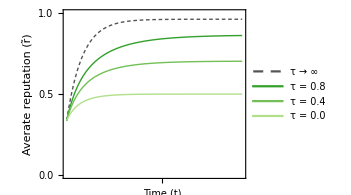

Exported Fig2F.pdf to ./plots/

```mathematica
p2F
savefig["Fig2F.pdf",p2F]
```

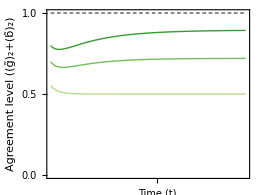

Exported Fig2G.pdf to ./plots/

```mathematica
p2G
savefig["Fig2G.pdf",p2G]
```

## 3.4: Critical gossip duration τ^* as a function of error rates (Fig S2)

### Functions

```mathematica
Clear[uaa,uee];
bb=5;cc=1; uaa=0.02;uee=0.02;τmax=1.2;
uees={0.02,0.12,0.22};
uaas={0.02,0.12,0.22};

pS2A=Plot[
Evaluate[τstarplot[b,c,ua,ue]/.{b->bb,c->cc,ue->#}&/@uees],{ua,0,0.5}
,PlotRange->{{0,0.5},{0,τmax}}
,PlotStyle->({Thick,#}&/@Reverse[blues])
,FrameTicks->MakeFrameTicks[2,2,0.5,τmax,0,0,5,3]
,FrameLabel->{ualabel,τstarlabel}
,PlotLegends->Placed[LineLegend[Automatic,(MakeLegendElement["u_e",#,12,{3,2}]&/@uees),Spacings->-0.1,LegendLayout->"ReversedColumn"],{Left,Top}]
,PlotTheme->"mk_plot"
,ImageSize->{220,220}
,AspectRatio->1
,Epilog->{Text[Style[MakeLegendElement["b/c",bb/cc,12,{1,0}],Darker[Gray]],{0.39,0.1},{-0.75,0.5}]}
];
pS2B=Plot[
Evaluate[τstarplot[b,c,ua,ue]/.{b->bb,c->cc,ua->#}&/@uaas],{ue,0,0.5}
,PlotRange->{{0,0.5},{0,τmax}}
,PlotStyle->({Thick,#}&/@Reverse[blues])
,FrameTicks->MakeFrameTicks[2,2,0.5,τmax,0,0,5,3]
,FrameLabel->{uelabel,None}
,PlotLegends->Placed[LineLegend[Automatic,(MakeLegendElement["u_a",#,12,{3,2}]&/@uaas),Spacings->-0.1,LegendLayout->"ReversedColumn"],{Left,Top}]
,PlotTheme->"mk_plot"
,ImageSize->{220,220}
,AspectRatio->1
,Epilog->{Text[Style[MakeLegendElement["b/c",bb/cc,12,{1,0}],Darker[Gray]],{0.39,0.1},{-0.75,0.5}]}
];
```

### Fig 2F and 2G

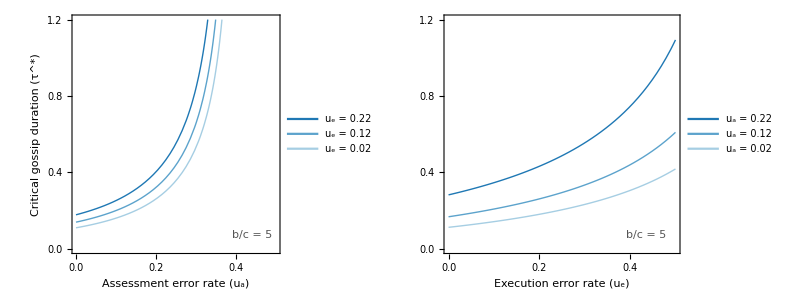

Exported FigS2.pdf to ./plots/

```mathematica
pS2=Grid[{{pS2A,pS2B}},Spacings->2]

savefig["FigS2.pdf",pS2]
```

## 3.5: Critical gossip duration (τ^*)_ALLD as a function of error rates (Fig S7)

### Functions

```mathematica
Clear[bmax,uaa,uee,cc,bb,pp,qq];
bb=3;cc=1; uaa=0.02;uee=0.02;τmax=1.2;
uees={0.02,0.12,0.22};
uaas={0.02,0.12,0.22};

τverrors[pp_,qq_]:=Module[{p1,p2,norm},

norm=If[pp==0,If[qq==1,"Stern Judging",If[qq==0,"Shunning"]],If[qq==1,"Simple Standing"]];

p1=Plot[
Evaluate[τALLDstar[b,c,ua,ue,p,q]/.{b->bb,c->cc,ue->#,p->pp,q->qq}&/@uees],{ua,0,0.5}
,PlotRange->{{0,0.5},{0,τmax}}
,PlotStyle->({Thick,#}&/@Reverse[blues])
,FrameTicks->MakeFrameTicks[2,2,0.5,τmax,0,0,5,3]
,FrameLabel->{ualabel,If[norm=="Stern Judging",τstarALLDlabel,""]}
(*,PlotLegends->If[norm=="Shunning",Placed[(Style["u_e = "<>ToString[#],FontSize->12]&/@uees),{Right,Bottom}],None]*)
,PlotLegends->If[norm=="Shunning",Placed[LineLegend[Automatic,(MakeLegendElement["u_e",#,12,{3,2}]&/@uaas),Spacings->-0.1,LegendLayout->"ReversedColumn"],{Right,Bottom}],None]
,PlotLabel->Style["Norm: "<>norm<>"",15,Black]
,PlotTheme->"mk_plot"
,ImageSize->{240,240}
,ImagePadding->{{50,10},{50,20}}
,AspectRatio->1
,Epilog->{Text[Style[If[norm=="Shunning",MakeLegendElement["b/c",bb/cc,12,{1,0}],""],Darker[Gray]],{0.005,0.07},{-0.75,0.5}]}
];
p2=Plot[
Evaluate[τALLDstar[b,c,ua,ue,p,q]/.{b->bb,c->cc,ua->#,p->pp,q->qq}&/@uaas],{ue,0,0.5}
,PlotRange->{{0,0.5},{0,τmax}}
,PlotStyle->({Thick,#}&/@Reverse[blues])
,FrameTicks->MakeFrameTicks[2,2,0.5,τmax,0,0,5,3]
,FrameLabel->{uelabel,If[norm=="Stern Judging",τstarALLDlabel,""]}
,PlotLegends->If[norm=="Shunning",Placed[LineLegend[Automatic,(MakeLegendElement["u_a",#,12,{3,2}]&/@uaas),Spacings->-0.1,LegendLayout->"ReversedColumn"],{Right,Bottom}],None]
,PlotLabel->Style["",15,Black]
,PlotTheme->"mk_plot"
,ImageSize->{240,240}
,ImagePadding->{{50,10},{50,20}}
,AspectRatio->1
,Epilog->{Text[Style[If[norm=="Shunning",MakeLegendElement["b/c",bb/cc,12,{1,0}],""],Darker[Gray]],{0.005,0.07},{-0.75,0.5}]}
];
Grid[{{p1},{p2}},Spacings->0]
]
```

### Fig S7

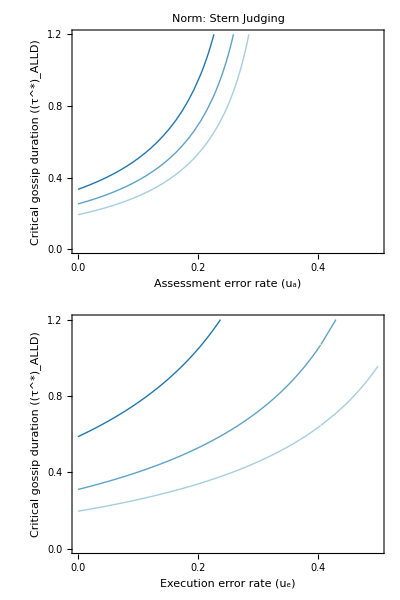
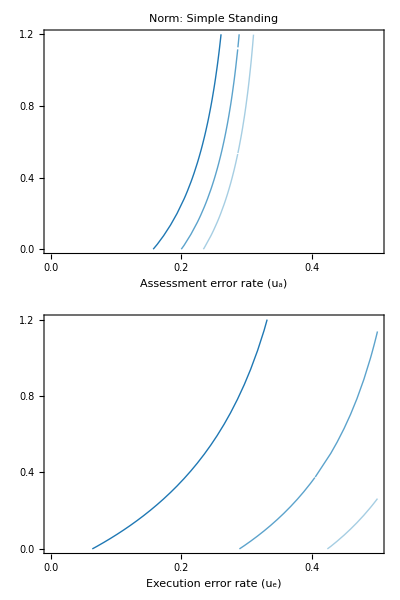
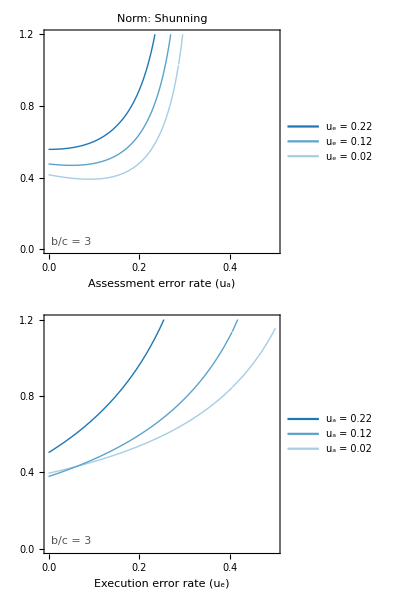
-Graphics- | -Graphics- | -Graphics-

Exported FigS7.pdf to ./plots/

```mathematica
pS7=Grid[{{τverrors[0,1],τverrors[1,1],τverrors[0,0]}},Spacings->-2]

savefig["FigS7.pdf",pS7]
```

## Part 4: Stability analysis with noisy, unbiased gossip (Figs 3 and S4)

## 4.1: Stability of the DISC equilibrium under Stern Judging (Fig 3A)

### Functions

```mathematica
(* reputation and replicator equations *)
setupalleqnswithnoise[p_,q_]:=(
ClearAll[eqDISC,eps,pgc,pbc,pgd,pbd,r,g2,b2,d2,g2gossip,b2gossip,d2gossip,pix,piy,piz,pi,drx,dry,drz,dfx,dfy,F,X,J,eigsDISC,eqnsrep,solrepDISC,Frep,Xrep,Jrep,eigsrepDISC];

eps:=(1-ua)(1-ue)+ua*ue;
pgc=eps;
pbc=p(eps-ua)+q(1-eps-ua)+ua;
pgd=ua;
pbd=q(1-2ua)+ua;

eqDISC={fx->0,fy->0};

(* large N approximation — assume U, V > 0; use these for analytical calculations *)
meanLarge[r0_,A_,B_,τ_]:=E^(-A*τ)(r0-B/A)+B/A;
varLarge[r0_,A_,B_,τ_]:=B/A(1-B/A)*1/(2*A+1)(1-E^(-(2*A+1)τ))+(1-(2B)/A)(r0-B/A)*1/(A+1)E^(-A*τ)*(1-E^(-(A+1)τ))-(r0-B/A)^2 E^(-2A*τ)(1-E^-τ);

(* agreement / disagreement terms, any N *)
g2Large[r0_,A_,B_,τ_]:=varLarge[r0,A,B,τ]+meanLarge[r0,A,B,τ]^2;
b2Large[r0_,A_,B_,τ_]:=1-2*meanLarge[r0,A,B,τ]+g2Large[r0,A,B,τ];
d2Large[r0_,A_,B_,τ_]:=meanLarge[r0,A,B,τ]-g2Large[r0,A,B,τ];

(* gossip -- summation is straightfoward because we assume the gossip processes are independent across individuals *)
g2gossip:=(fx*g2Large[rx,A,B,τ]+fy*g2Large[ry,A,B,τ] +(1-fx-fy)*g2Large[rz,A,B,τ]);
b2gossip:=(fx*b2Large[rx,A,B,τ]+fy*b2Large[ry,A,B,τ] +(1-fx-fy)*b2Large[rz,A,B,τ]);
d2gossip:=(fx*d2Large[rx,A,B,τ]+fy*d2Large[ry,A,B,τ] +(1-fx-fy)*d2Large[rz,A,B,τ]);

(* reputation dynamics *)
r:=(fx*rx+fy*ry +(1-fx-fy)*rz);
drx:=δ(r*pgc+(1-r)*pbc-rx);
dry:=δ(r*pgd+(1-r)*pbd-ry);
drz:=δ((g2gossip*pgc+d2gossip*(pbc+pgd)+b2gossip*pbd)-rz);

(* strategy dynamics -- rx, ry, rz are the equilibrium reputations *)
pix:=(1-ue)(b(fx+(1-fx-fy)*rx)-c);
piy:=(1-ue)(b(fx+(1-fx-fy)*ry));
piz:=(1-ue)(b(fx+(1-fx-fy)*rz)-c*r);
pi:=fx*pix+fy*piy+(1-fx-fy)*piz;

dfx:=fx*(pix-pi);
dfy:=fy*(piy-pi);

(* strategy equilibrium *)
F:={dfx,dfy};
X:={fx,fy};
J:=D[F,{X}];
eigsDISC:=Eigenvalues[J//.eqDISC];
eigsDISCforALLC:=eigsDISC[[1]];(* see cell below *) 
eigsDISCforALLD:=eigsDISC[[2]];

(* reputation equilibrium *)
eqnsrep:={drx==0,dry==0,drz==0};
solrepDISC:=Solve[(eqnsrep//.eqDISC),{rx,ry,rz}];
Frep:={drx,dry,drz};
Xrep:={rx,ry,rz};
Jrep:=D[Frep,{Xrep}];
eigsrepDISC:=Eigenvalues[Jrep//.eqDISC]
)

(*(* select valid solutions *)
Clear[tol];tol=10^-30;

selectrepsol[sol_List]:=Module[{validsol},
validsol=Select[sol,And@@Thread[Abs[Im[#]]<tol&&0-tol*0<=#<=1+tol*0&/@Values[#]]&];
If[Length[validsol]==0,
Print["No valid solution found!"];Return[Null],
If[Length[validsol]==1,
Return[validsol],
If[Length[validsol]>1,
Return[validsol]
]]]];*)

(* functions to compute critical thresholds numerically *)
criticalτ2[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_]:=Module[{τstar,τ1,τ2,eigsDISCeval},
(* rsoln is the (true) analytical solution to the reputation equations at the DISC equilibrium *)
eigsDISCeval=(eigsDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc,A->AA,B->BB}//FullSimplify);

(* find the zeroes corresponding to each eigenvalue, assuming eigenvalues are real (only checking sign) *) 
τ1=Quiet@Flatten[FindRoot[0.==FullSimplify[eigsDISCeval[[1]]],{{τ,0.01,0.,5.}}],1];
τ2=Quiet@Flatten[FindRoot[0.==FullSimplify[eigsDISCeval[[2]]],{{τ,0.01,0.,5.}}],1];

(* select only solutions that are actually zeroes *) 
τ1=Select[τ1,Chop[eigsDISCeval[[1]]/.#]==0. &];
τ2=Select[τ2,Chop[eigsDISCeval[[2]]/.#]==0. &];
If[Length@τ1>1||Length@τ2>1,Print["One of the eigenvalues has two zeroes; check values"]];

(* critical threshold is the higher of the two bounds because both eigenvalues need to be negative *) 
τstar=Max[{τ/.({τ1,τ2}/. {}->Nothing)}];
Return[τstar]
]

criticalτ2ALLD[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_]:=Module[{τstar,τ1,τ2,eigsDISCeval},
eigsDISCeval=(eigsDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc,A->AA,B->BB}//FullSimplify);

(* we only care about eigsDISCeval[[2]] for stability against ALLD *) 
τ1={};
If[NumericQ[FullSimplify[eigsDISCeval[[2]]]],
τ2={},
τ2=Quiet@Flatten[FindRoot[0.==FullSimplify[eigsDISCeval[[2]]],{{τ,0.01,0.,5.}}],1]
];

(* select only solutions that are actually zeroes *) 
τ1={};
τ2=Select[τ2,Chop[eigsDISCeval[[2]]/.#]==0. &];
If[Length@τ1>1||Length@τ2>1,Print["One of the eigenvalues has two zeroes; check values"]];

(* critical threshold is the higher of the two bounds because both eigenvalues need to be negative *) 
τstar=Max[{τ/.({τ1,τ2}/. {}->Nothing)}];
Return[τstar]
]

(* other functions *)
scalebias[A_,B_]:=2(B/A-1/2) (* equivalent to 2*(V/(U+V)-1/2) *)
bcstar[ua_,ue_]:=(1/((1-2 ua) (1-ue)));

eτstar[b_,c_,ua_,ue_]:=2*(1-1/2*(b/c)/((b/c)-1/(2(1-ua))))((b/c)/((b/c)-1/((1-2 ua) (1-ue))));
τstar[b_,c_,ua_,ue_]:=Log[eτstar[b,c,ua,ue]];
τstarplot[b_,c_,ua_,ue_]:=If[(b/c>bcstar[ua,ue])&&(eτstar[b,c,ua,ue]>0),Log[eτstar[b,c,ua,ue]],If[b/c>bcstar[ua,ue],Log[eτstar[b,c,ua,ue]],Undefined]];

eτALLDstar[b_,c_,ua_,ue_,p_,q_]:=(1-p+q)(1-((ua+q (1-2 ua))/(1+q (1-2 ua)))(b/c)/((b/c)-1/(1+q (1-2 ua))))((b/c)/((b/c)-1/((1-2 ua) (1-ue))));
τALLDstar[b_,c_,ua_,ue_,p_,q_]:=Log[eτALLDstar[b,c,ua,ue,p,q]];
τALLDstarplot[b_,c_,ua_,ue_,p_,q_]:=If[(b/c>bcstar[ua,ue])&&(eτALLDstar[b,c,ua,ue,p,q]>1),Log[eτALLDstar[b,c,ua,ue,p,q]],If[(b/c>bcstar[ua,ue]),Log[eτALLDstar[b,c,ua,ue,p,q]],Undefined]];
```

```mathematica
(* Fig 3A *)
plotcriticalτ[AAs_,bmax_,τmax_,cc_,uaa_,uee_,inc_?NumericQ,verbose_:False]:=Module[{p1,p2,data1,data2,data3,rsol,norm,eqns},

(* set norm *)
Print["This function is for SJ norm only!"];
norm="SJ";setupalleqnswithnoise[0,1]; (* SJ *)

(* simplify equations *)
eqns={drx==0,dry==0,drz==0}/.{δ->1};

(* solve for rx, ry, rz *)
rsol=Solve[(eqns//.eqDISC),{rx,ry,rz}];

(* check sols numerically if verbose = TRUE*)
If[verbose,
Print["Numerical example: ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}," vs ",rsol[[2]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}];
Print["The actual solution is ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}]
];

(* rsol[[1]] is the actual solution *)
rsol=rsol[[1]];

(* data points to plot *) 
data1=Table[{bb,criticalτ2[rsol,bb,cc,uaa,uee,AAs[[1]],AAs[[1]]/2.]},{bb,1.,bmax+bmax/inc*1,bmax/inc*1}];
data2=Table[{bb,criticalτ2[rsol,bb,cc,uaa,uee,AAs[[2]],AAs[[2]]/2.]},{bb,1.,bmax+bmax/inc*1,bmax/inc*1}];
data3=Table[{bb,criticalτ2[rsol,bb,cc,uaa,uee,AAs[[3]],AAs[[3]]/2.]},{bb,1.,bmax+bmax/inc*1,bmax/inc*1}];

(* plot *) 
p1=ListLinePlot[
{data1,data2,data3}
,PlotStyle->({Thick,#}&/@{inferno4,inferno5,inferno6})
,PlotRange->{{1,bmax},{0.,τmax}}
,PlotLegends->Placed[
LineLegend[{inferno3,inferno4,inferno5,inferno6}
(*,(Style[#,10]&/@Flatten[{" μ + ν = 0.0",(" μ + ν = "<>ToString@NumberForm[#,{2,1}]&/@AAs)}])*)
,(MakeLegendElement["μ + ν",#,11,{2,1},0.1]&/@Flatten[{0.0,AAs}])
,LegendMarkerSize->11,Spacings->-0.2,LegendLabel->Style["Noise level",10]
,LegendLayout->"ReversedColumn"]
,{Right,Top}]
];
p2=Plot[τstarplot[bb,cc,uaa,uee],{bb,1.,bmax}
,FrameLabel->{bclabel,τstarlabel}
,PlotStyle->{Thick,inferno3}
,PlotRange->{{1,bmax},{0.,τmax}}
,PlotTheme->"mk_plot"
,FrameTicks->MakeFrameTicks[1,2,bmax,τmax,1,0,3,3]
,ImageSize->{205*1.5,205}
,AspectRatio->1/2
,GridLines->None
];
Show[p2,p1]
]

(* Fig S4 *)
plotcriticalτALLD[AAs_,bmax_,τmax_,cc_,uaa_,uee_,norm_?StringQ,inc_?NumericQ,verbose_:False]:=Module[{p1,p2,data1,data2,data3,rsol,eqns,pp,qq},

(* set norm-related paramters *)
Print["This function is for any norm; current norm is ",norm];
If[norm=="SJ",pp=0;qq=1,
If[norm=="SS",pp=1;qq=1,
If[norm=="SH",pp=0;qq=0]]];
setupalleqnswithnoise[pp,qq];

(* simplify equations *)
eqns={drx==0,dry==0,drz==0}/.{δ->1};

(* solve for rx, ry, rz *)
rsol=Solve[(eqns//.eqDISC),{rx,ry,rz}];

(* check sols numerically if verbose = TRUE*)
If[verbose,
Print["Numerical example: ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}," vs ",rsol[[2]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}];
Print["The actual solution is ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}]
];

(* rsol[[1]] is the actual solution *)
rsol=rsol[[1]];

(* data points to plot *) 
data1=Table[{bb,criticalτ2ALLD[rsol,bb,cc,uaa,uee,AAs[[1]],AAs[[1]]/2.]},{bb,1.,bmax+bmax/inc*1,bmax/inc*1}];
data2=Table[{bb,criticalτ2ALLD[rsol,bb,cc,uaa,uee,AAs[[2]],AAs[[2]]/2.]},{bb,1.,bmax+bmax/inc*1,bmax/inc*1}];
data3=Table[{bb,criticalτ2ALLD[rsol,bb,cc,uaa,uee,AAs[[3]],AAs[[3]]/2.]},{bb,1.,bmax+bmax/inc*1,bmax/inc*1}];

(* plot *) 
p1=ListLinePlot[
{data1,data2,data3}
,PlotStyle->({Thick,#}&/@{inferno4,inferno5,inferno6})
,PlotRange->{{1,bmax},{0.,τmax}}
,PlotLegends->Placed[
LineLegend[{inferno3,inferno4,inferno5,inferno6}
,(MakeLegendElement["μ + ν",#,11,If[norm=="SS",{3,2},{2,1}],0.1]&/@Flatten[{0.0,AAs}])
,LegendMarkerSize->10,Spacings->-0.2,LegendLabel->Style["Noise level",10]
,LegendLayout->"ReversedColumn"]
,{Right,Top}]
];
p2=Plot[τALLDstarplot[bb,cc,uaa,uee,pp,qq],{bb,1.,bmax}
,FrameLabel->{bclabel,τstarALLDlabel}
,PlotStyle->{Thick,inferno3}
,PlotRange->{{1,bmax},{0.,τmax}}
,PlotTheme->"mk_plot"
,FrameTicks->MakeFrameTicks[If[norm=="SS",2,1],2,bmax,τmax,1,0,3,3]
,ImageSize->{205*1.5,205*1.25}
,AspectRatio->2/3
,GridLines->None
];
Show[p2,p1]
]
```

### Fig 3A

This function is for SJ norm only!

Numerical example: {rx→0.640851,ry→0.353281,rz→0.652833} vs {rx→18.3885,ry→-18.1338,rz→19.9102}

The actual solution is {rx→0.640851,ry→0.353281,rz→0.652833}

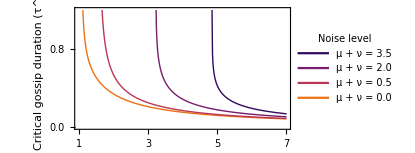

Exported Fig3A.pdf to ./plots/

```mathematica
Clear[bmax,τpmax,cc,uaa,uee,AAs,inc];

bmax=7;τpmax=1.2;cc=1.;uaa=0.02;uee=0.02;AAs={0.5,2.0,3.5};inc=500;
p3A=plotcriticalτ[AAs,bmax,τpmax,cc,uaa,uee,inc,True]

savefig["Fig3A.pdf",p3A]
```

## 4.2: Stability of the DISC equilibrium against ALLD under any norm (p, q) (Fig S4)

### Fig S4A

This function is for any norm; current norm is SS

Numerical example: {rx→0.964407,ry→0.200329,rz→0.812158} vs {rx→0.225171,ry→-36.7614,rz→39.314}

The actual solution is {rx→0.964407,ry→0.200329,rz→0.812158}

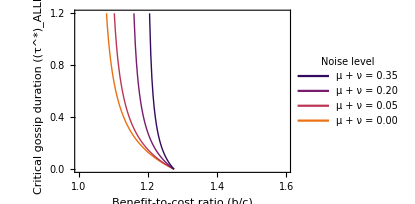

Exported FigS4A.pdf in ./plots/

```mathematica
Clear[bmax,τmax,cc,uaa,uee,AAs,norm,inc];
bmax=1.6;τmax=1.2;cc=1.;uaa=0.02;uee=0.02;AAs={0.5,2.0,3.5}/10;norm="SS";inc=500;
pS4A=plotcriticalτALLD[AAs,bmax,τmax,cc,uaa,uee,norm,inc,True]

savefig["FigS4A.pdf",pS4A]
```

### Fig S4B

This function is for any norm; current norm is SJ

Numerical example: {rx→0.640851,ry→0.353281,rz→0.652833} vs {rx→18.3885,ry→-18.1338,rz→19.9102}

The actual solution is {rx→0.640851,ry→0.353281,rz→0.652833}

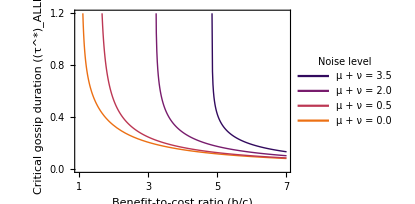

Exported FigS4B.pdf in ./plots/

```mathematica
Clear[bmax,τmax,cc,uaa,uee,AAs,norm,inc];
bmax=7;τmax=1.2;cc=1.;uaa=0.02;uee=0.02;AAs={0.5,2.0,3.5};norm="SJ";inc=500;
pS4B=plotcriticalτALLD[AAs,bmax,τmax,cc,uaa,uee,norm,inc,True]

savefig["FigS4B.pdf",pS4B]
```

### Fig S4C

This function is for any norm; current norm is SH

Numerical example: {rx→0.270974,ry→0.02,rz→0.266766} vs {rx→26.9375,ry→0.02,rz→28.6112}

The actual solution is {rx→0.270974,ry→0.02,rz→0.266766}

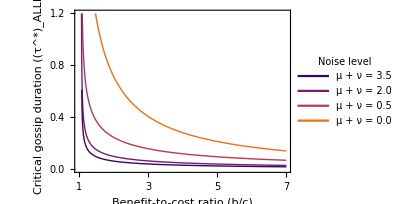

Exported FigS4C.pdf in ./plots/

```mathematica
Clear[bmax,τmax,cc,uaa,uee,AAs,norm,inc];
bmax=7;τmax=1.2;cc=1.;uaa=0.02;uee=0.02;AAs={0.5,2.0,3.5};norm="SH";inc=750;
pS4C=plotcriticalτALLD[AAs,bmax,τmax,cc,uaa,uee,norm,inc,True]

savefig["FigS4C.pdf",pS4C]
```

## 4.3: Average reputations and agreement levels at the DISC equilibrium under Stern Judging (Figs 3B–C)

### Functions

```mathematica
(* reputation and replicator equations *)
setupalleqnswithnoise2[p_,q_]:=(
ClearAll[eqDISC,eps,pgc,pbc,pgd,pbd,r,g2,b2,d2,g2gossip,b2gossip,d2gossip,pix,piy,piz,pi,drx,dry,drz,dfx,dfy,F,X,J,eigsDISC,eqnsrep,solrepDISC,Frep,Xrep,Jrep,eigsrepDISC];

eps:=(1-ua)(1-ue)+ua*ue;
pgc=eps;
pbc=p(eps-ua)+q(1-eps-ua)+ua;
pgd=ua;
pbd=q(1-2ua)+ua;

eqDISC={fx->0,fy->0};

(* large N approximation — includes U, V = 0; use these for numercal plots *)
meanLarge[r0_,U_,V_,tprime_]:=If[U≠0||V≠0,E^(-(U+V)tprime)(r0-V/(U+V))+V/(U+V),r0];
varLarge[r0_,U_,V_,tprime_]:=If[U≠0||V≠0,V/(U+V)(1-V/(U+V))*1/(2(U+V)+1)(1-E^(-(2(U+V)+1)tprime))+(1-(2V)/(U+V))(r0-V/(U+V))*1/((U+V)+1)E^(-(U+V)tprime)*(1-E^(-((U+V)+1)tprime))-(r0-V/(U+V))^2 E^(-2(U+V)tprime)(1-E^-tprime),r0(1-r0)(1-E^-tprime)];

(* agreement / disagreement terms, any N *)
g2Large[r0_,U_,V_,τ_]:=varLarge[r0,U,V,τ]+meanLarge[r0,U,V,τ]^2;
b2Large[r0_,U_,V_,τ_]:=1-2*meanLarge[r0,U,V,τ]+g2Large[r0,U,V,τ];
d2Large[r0_,U_,V_,τ_]:=meanLarge[r0,U,V,τ]-g2Large[r0,U,V,τ];

(* gossip  *)
g2gossip:=(fx*g2Large[rx,U,V,τ]+fy*g2Large[ry,U,V,τ] +(1-fx-fy)*g2Large[rz,U,V,τ]);
b2gossip:=(fx*b2Large[rx,U,V,τ]+fy*b2Large[ry,U,V,τ] +(1-fx-fy)*b2Large[rz,U,V,τ]);
d2gossip:=(fx*d2Large[rx,U,V,τ]+fy*d2Large[ry,U,V,τ] +(1-fx-fy)*d2Large[rz,U,V,τ]);

(* reputation dynamics *)
r:=(fx*rx+fy*ry +(1-fx-fy)*rz);
drx:=δ(r*pgc+(1-r)*pbc-rx);
dry:=δ(r*pgd+(1-r)*pbd-ry);
drz:=δ((g2gossip*pgc+d2gossip*(pbc+pgd)+b2gossip*pbd)-rz);

(* strategy dynamics -- rx, ry, rz are the equilibrium reputations *)
pix:=(1-ue)(b(fx+(1-fx-fy)*rx)-c);
piy:=(1-ue)(b(fx+(1-fx-fy)*ry));
piz:=(1-ue)(b(fx+(1-fx-fy)*rz)-c*r);
pi:=fx*pix+fy*piy+(1-fx-fy)*piz;

dfx:=fx*(pix-pi);
dfy:=fy*(piy-pi);

(* strategy equilibrium *)
F:={dfx,dfy};
X:={fx,fy};
J:=D[F,{X}];
eigsDISC:=Eigenvalues[J//.eqDISC];
eigsDISCforALLC:=eigsDISC[[1]];(* see cell below *) 
eigsDISCforALLD:=eigsDISC[[2]];

(* reputation equilibrium *)
eqnsrep:={drx==0,dry==0,drz==0};
solrepDISC:=Solve[(eqnsrep//.eqDISC),{rx,ry,rz}];
Frep:={drx,dry,drz};
Xrep:={rx,ry,rz};
Jrep:=D[Frep,{Xrep}];
eigsrepDISC:=Eigenvalues[Jrep//.eqDISC]
)

Clear[tol];tol=10^-30;

selectrepsol[sol_List]:=Module[{validsol},
validsol=Select[sol,And@@Thread[Abs[Im[#]]<tol&&0-tol*0<=#<=1+tol*0&/@Values[#]]&];
If[Length[validsol]==0,
Print["No valid solution found!"];Return[Null],
If[Length[validsol]==1,
Return[validsol],
If[Length[validsol]>1,
Return[validsol]
]]]];

checksign[eigs_]:=If[Length@eigs>1,Boole@AllTrue[eigs,Re[#]<0&],Boole[Re[eigs]<0]];

stabilityrepDISC[rsoln_,uaa_,uee_,δδ_,ττ_,UU_,VV_,pp_,qq_]:=eigsrepDISC/.{rx->rsoln[[1]],ry->rsoln[[2]],rz->rsoln[[3]]}//.{ua->uaa,ue->uee,δ->δδ,τ->ττ,U->UU,V->VV,p->pp,q->qq}//checksign

stabilityDISC[rsoln_,bb_,cc_,uaa_,uee_,pp_,qq_]:=eigsDISC/.{rx->rsoln[[1]],ry->rsoln[[2]],rz->rsoln[[3]]}//.{b->bb,c->cc,ua->uaa,ue->uee,p->pp,q->qq}//checksign

stabilityDISCforALLC[rsoln_,bb_,cc_,uaa_,uee_,pp_,qq_]:=eigsDISCforALLC/.{rx->rsoln[[1]],ry->rsoln[[2]],rz->rsoln[[3]]}//.{b->bb,c->cc,ua->uaa,ue->uee,p->pp,q->qq}//checksign

stabilityDISCforALLD[rsoln_,bb_,cc_,uaa_,uee_,pp_,qq_]:=eigsDISCforALLD/.{rx->rsoln[[1]],ry->rsoln[[2]],rz->rsoln[[3]]}//.{b->bb,c->cc,ua->uaa,ue->uee,p->pp,q->qq}//checksign

stabilitydata[bb_,cc_,uaa_,uee_,δδ_,UU_,VV_,norm_,τmax_,type_:"full"]:=Module[{pp,qq},
If[norm=="SC"||norm=="SS",pp=1,pp=0];
If[norm=="SJ"||norm=="SS",qq=1,qq=0];
setupalleqnswithnoise2[pp,qq];
(* return stability data *) 
Return[Flatten[Table[
{ττ,
({rx,ry,rz}/.#),
stabilityrepDISC[({rx,ry,rz}/.#),uaa,uee,δδ,ττ,UU,VV,pp,qq],
If[type=="full",stabilityDISC[({rx,ry,rz}/.#),bb,cc,uaa,uee,pp,qq]
,If[type=="ALLC",stabilityDISCforALLC[({rx,ry,rz}/.#),bb,cc,uaa,uee,pp,qq]
,If[type=="ALLD",stabilityDISCforALLD[({rx,ry,rz}/.#),bb,cc,uaa,uee,pp,qq]]]],
({g2gossip,b2gossip,d2gossip}//.eqDISC/.#/.{τ->ττ,U->UU,V->VV}),
({pix,piy,piz}//.eqDISC/.#/.{b->bb,c->cc,ue->uee(*,γ->γγ*)})
}&/@(selectrepsol @ NSolve[{drx==0,dry==0,drz==0}//.{ua->uaa,ue->uee,δ->δδ,τ->ττ,U->UU,V->VV}//.eqDISC,{rx,ry,rz},Reals]),
{ττ,0.,τmax,τmax/50}
],1]]
]

plotrepsandagreement[bb_,cc_,uaa_,uee_,δδ_,UUVVs_,norm_,τmax_,type_,fs_:6]:=Module[{data1,dataSS1,dataSU1,data2,dataSS2,dataSU2,data3,dataSS3,dataSU3,data0,dataSS0,dataSU0,p1,p2,agreementbefore,agreementafter},

(* generate data to plot *)
data1=stabilitydata[bb,cc,uaa,uee,δδ,UUVVs[[1,1]],UUVVs[[1,2]],norm,τmax,type];
dataSS1=Append[Select[data1,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,1]&],{None,{None,None,None}}];dataSU1=Append[Select[data1,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,0]&],{None,{None,None,None}}];

data2=stabilitydata[bb,cc,uaa,uee,δδ,UUVVs[[2,1]],UUVVs[[2,2]],norm,τmax,type];
dataSS2=Append[Select[data2,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,1]&],{None,{None,None,None}}];dataSU2=Append[Select[data2,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,0]&],{None,{None,None,None}}];

data3=stabilitydata[bb,cc,uaa,uee,δδ,UUVVs[[3,1]],UUVVs[[3,2]],norm,τmax,type];
dataSS3=Append[Select[data3,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,1]&],{None,{None,None,None}}];dataSU3=Append[Select[data3,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,0]&],{None,{None,None,None}}];

data0=stabilitydata[bb,cc,uaa,uee,δδ,UUVVs[[4,1]],UUVVs[[4,2]],norm,τmax,type];
dataSS0=Append[Select[data0,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,1]&],{None,{None,None,None}}];dataSU0=Append[Select[data0,MatchQ[#1⟦3⟧,1]&&MatchQ[#1⟦4⟧,0]&],{None,{None,None,None}}];

agreementbefore[rz_,τ_]:=rz^2+(1-rz)^2;
agreementafter[rz_,τ_,U_,V_]:=g2Large[rz,U,V,τ]+b2Large[rz,U,V,τ];

(* plot reputations and color by stability *) 
p1=ListLinePlot[{
Table[{dataSS0⟦i,1⟧,dataSS0⟦i,2,3⟧},{i,1,Length[dataSS0]}],Table[{dataSU0⟦i,1⟧,dataSU0⟦i,2,3⟧},{i,1,Length[dataSU0]}]
,Table[{dataSS1⟦i,1⟧,dataSS1⟦i,2,3⟧},{i,1,Length[dataSS1]}],Table[{dataSU1⟦i,1⟧,dataSU1⟦i,2,3⟧},{i,1,Length[dataSU1]}]
,Table[{dataSS2⟦i,1⟧,dataSS2⟦i,2,3⟧},{i,1,Length[dataSS2]}],Table[{dataSU2⟦i,1⟧,dataSU2⟦i,2,3⟧},{i,1,Length[dataSU2]}]
,Table[{dataSS3⟦i,1⟧,dataSS3⟦i,2,3⟧},{i,1,Length[dataSS3]}],Table[{dataSU3⟦i,1⟧,dataSU3⟦i,2,3⟧},{i,1,Length[dataSU3]}]
}
,PlotRange->{{0,τmax},{0.5,1.}}
,PlotStyle->Flatten[Table[{Thick,color,dash},{color,{inferno3,inferno4,inferno5,inferno6}},{dash,{Dashing[None],Dashed}}],1]
,FrameLabel->{τlabel,replabel}
,FrameTicks->MakeFrameTicks[2,3,0.6,1.,0,0.5,3,2]
,PlotTheme->"mk_plot"
,ImageSize->{175,225}
,ImagePadding->{{65,10},{65,10}}
,AspectRatio->3/2
,GridLines->None
];
p2=ListLinePlot[
{
Table[{dataSS0⟦i,1⟧,agreementafter[dataSS0⟦i,2,3⟧,dataSS0⟦i,1⟧,UUVVs⟦4,1⟧,UUVVs⟦4,2⟧]},{i,1,Length[dataSS0]}]
,Table[{dataSU0⟦i,1⟧,agreementafter[dataSU0⟦i,2,3⟧,dataSU0⟦i,1⟧,UUVVs⟦4,1⟧,UUVVs⟦4,2⟧]},{i,1,Length[dataSU0]}]
,Table[{dataSS1⟦i,1⟧,agreementafter[dataSS1⟦i,2,3⟧,dataSS1⟦i,1⟧,UUVVs⟦1,1⟧,UUVVs⟦1,2⟧]},{i,1,Length[dataSS1]}]
,Table[{dataSU1⟦i,1⟧,agreementafter[dataSU1⟦i,2,3⟧,dataSU1⟦i,1⟧,UUVVs⟦1,1⟧,UUVVs⟦1,2⟧]},{i,1,Length[dataSU1]}]
,Table[{dataSS2⟦i,1⟧,agreementafter[dataSS2⟦i,2,3⟧,dataSS2⟦i,1⟧,UUVVs⟦2,1⟧,UUVVs⟦2,2⟧]},{i,1,Length[dataSS2]}]
,Table[{dataSU2⟦i,1⟧,agreementafter[dataSU2⟦i,2,3⟧,dataSU2⟦i,1⟧,UUVVs⟦2,1⟧,UUVVs⟦2,2⟧]},{i,1,Length[dataSU2]}]
,Table[{dataSS3⟦i,1⟧,agreementafter[dataSS3⟦i,2,3⟧,dataSS3⟦i,1⟧,UUVVs⟦3,1⟧,UUVVs⟦3,2⟧]},{i,1,Length[dataSS3]}]
,Table[{dataSU3⟦i,1⟧,agreementafter[dataSU3⟦i,2,3⟧,dataSU3⟦i,1⟧,UUVVs⟦3,1⟧,UUVVs⟦3,2⟧]},{i,1,Length[dataSU3]}]
}
,PlotRange->{{0,τmax},{0.5,1.}}
,PlotStyle->Flatten[Table[{Thick,color,dash},{color,{inferno3,inferno4,inferno5,inferno6}},{dash,{Dashing[None],Dashed}}],1]
,FrameLabel->{τlabel,agreelabel}
,FrameTicks->MakeFrameTicks[2,3,0.6,1.,0,0.5,3,2]
,PlotTheme->"mk_plot"
,ImageSize->{175,225}
,ImagePadding->{{65,10},{65,10}}
,AspectRatio->3/2
,GridLines->None
];
Grid[{{p2,p1}},Spacings->0.5]
]
```

### Figs 3B,C

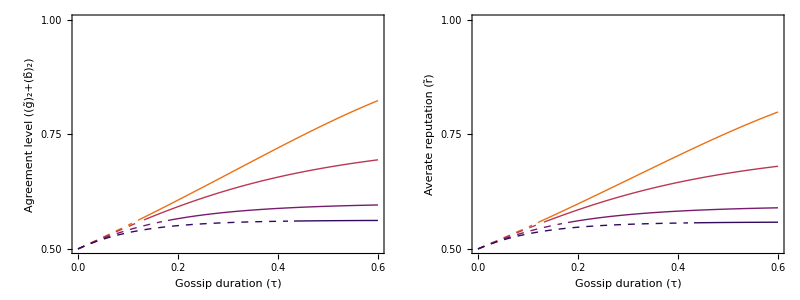

Exported Fig3B+C.pdf to ./plots/

```mathematica
Clear[uaa,uee,bb,cc,δδ,UU,VV,τmax,norm];
uaa=.02;uee=.02;bb=5;cc=1;δδ=1;τmax=1.2/2;fs=5;
UUVVs={{0.5,0.5}/2.,{2.,2.}/2.,{3.5,3.5}/2.,{0,0}};
norms={"SJ"};type = "full";

p3BC=plotrepsandagreement[bb,cc,uaa,uee,δδ,UUVVs,norms[[1]],τmax,type,fs]

savefig["Fig3B+C.pdf",p3BC]
```

## Part 5: Stability analysis with biased gossip (Figs 4, S5, and S6)

## 5.1: Stability of the DISC equilibrium under Stern Judging (Figs 4A–C)

### Functions

```mathematica
(* Fig 4 *)
plotcriticalτvβ[Amax_,τmax_,bb_,cc_,uaa_,uee_,inc_?NumericQ,verbose_:False]:=Module[{p1,p2,color,data1,data2,data3,rsol,norm,eqns},

If[Amax==0.5,color=inferno4,
If[Amax==2.0,color=inferno5,
If[Amax==3.5,color=inferno6]]];

(* set norm *)
If[verbose,Print["This function is for SJ norm only!"]];
norm="SJ";setupalleqnswithnoise[0,1]; (* SJ *)

(* simplify equations *)
eqns={drx==0,dry==0,drz==0}/.{δ->1};

(* solve for rx, ry, rz *)
rsol=Solve[(eqns//.eqDISC),{rx,ry,rz}];

(* check sols numerically if verbose = TRUE*)
If[verbose,
Print["Numerical example: ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}," vs ",rsol[[2]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}];
Print["The actual solution is ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}]
];

(* rsol[[1]] is the actual solution *)
rsol=rsol[[1]];

p1=ListLinePlot[
Table[{BB,criticalτ2[rsol,bb,cc,uaa,uee,Amax,BB]},{BB,0.,Amax,Amax*1./inc}]
,Filling->Top
,PlotStyle->{Thick,color}
,PlotRange->{{0,Amax},{0.,τmax}}
,FrameLabel->{betalabel,If[Amax==0.5,τstarlabel,""]}
,PlotTheme->"mk_plot"
,PlotLabel->Style["μ + ν = "<>ToString[NumberForm[Amax,{2,1}]],Black,13]
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,τmax,5]),None},{(({#,NumberForm[scalebias[Amax,#],{1,0},NumberPoint->""],{0,0.02}})&/@Subdivide[0,Amax,2]),None}}
,ImageSize->{225,225}
,ImagePadding->{{50,5},{50,5}}
,GridLines->None
,AspectRatio->1
,Prolog->{
{Thin,Dashed,Darker[Gray],Line[{{Amax/2.,-0.1},{Amax/2.,τmax}}]}
,{AbsolutePointSize[1.6],inferno3,Point@Tuples[{Range[0,Amax,Amax/40],ConstantArray[τstarplot[bb,cc,uaa,uee],40]}]}
}
,Epilog->{
Text[If[Amax==0.5,Style["⟵ Negative bias",Darker[Gray],9],""],{0.,0.},{-1,-1}]
,Text[If[Amax==0.5,Style["Positive bias ⟶",Darker[Gray],9],""],{Amax,0.},{1,-1}]
,Text[If[Amax==0.5,Row[{Style["τ^*",FontFamily->"Times New Roman",inferno3,10]
,Style[" without noise",FontFamily->"Arial",inferno3,9]}
,BaselinePosition->Center]],{0.,τmax*0.25},{-1,1}]
,Text[If[Amax==0.5,Style["DISC stable",color,11],""],{0.49,0.49},{1,1}]
}
];
Show@p1
]
```

### Fig 4

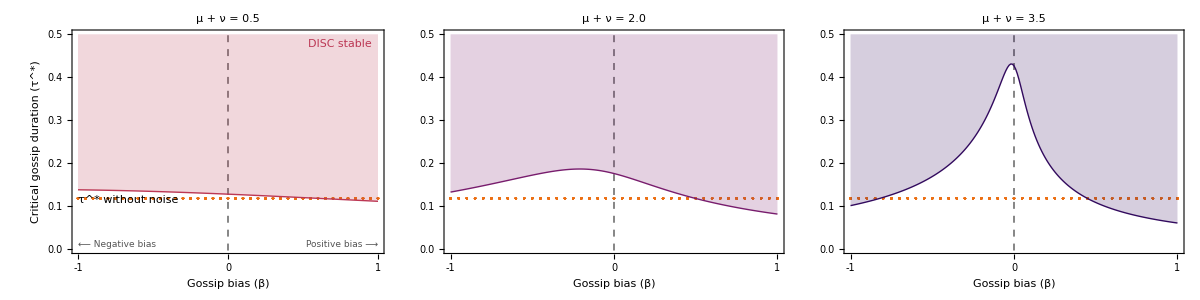

Exported Fig4.pdf to ./plots/

```mathematica
Clear[Amax,τmax];τmax=0.5;bb=5.;cc=1.;uaa=0.02;uee=0.02;inc=200;
p4=Grid[{plotcriticalτvβ[#,τmax,bb,cc,uaa,uee,inc,False]&/@{0.5,2.,3.5}},Spacings->0.0]

savefig["Fig4.pdf",p4]
```

## 5.2: Agreement/disagreement terms at the DISC equilibrium under Stern Judging (Figs S5)

### Functions

```mathematica
Clear[bb,cc,uaa,uee,bbb,ccc,uaaa,ueee,Amax,inc,τmax]

plotg2b2d2[Amax_,τmax_,bbb_,ccc_,uaaa_,ueee_,norm_?StringQ,inc_?NumericQ,verbose_:False]:=Module[
{p1,p2,p3,data1,data2,data3,rsol,eqns,pp,qq,plotg2eq,plotb2eq,plotd2eq,plotg2gossip,plotb2gossip,plotd2gossip},

(* set norm-related paramters *)
If[verbose,Print["This function is for any norm; current norm is ",norm]];
If[norm=="SJ",pp=0;qq=1,
If[norm=="SS",pp=1;qq=1,
If[norm=="SH",pp=0;qq=0]]];

Clear[g2gossip,b2gossip,d2gossip];setupalleqnswithnoise[pp,qq];

(*(* using the equilibrium reputations *)
plotg2eq[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_,ττ_]:=(fx*rx^2+fy*ry^2+(1-fx-fy)*rz^2)/.eqDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc}/.{A->AA,B->BB,τ->ττ};
plotb2eq[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_,ττ_]:=(fx*(1-rx)^2+fy*(1-ry)^2+(1-fx-fy)*(1-rz)^2)/.eqDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc}/.{A->AA,B->BB,τ->ττ};
plotd2eq[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_,ττ_]:=(fx*rx(1-rx)+fy*ry(1-ry)+(1-fx-fy)*rz(1-rz))/.eqDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc}/.{A->AA,B->BB,τ->ττ};*)

(* gossip process only, but starting from the equilibrium reputations *)
plotg2gossip[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_,ττ_]:=g2gossip/.eqDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc}/.{A->AA,B->BB,τ->ττ};
plotb2gossip[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_,ττ_]:=b2gossip/.eqDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc}/.{A->AA,B->BB,τ->ττ};
plotd2gossip[rsoln_,bb_,cc_,uaa_,uee_,AA_,BB_,ττ_]:=d2gossip/.eqDISC/.rsoln/.{ua->uaa,ue->uee,b->bb,c->cc}/.{A->AA,B->BB,τ->ττ};

(* simplify equations *)
eqns={drx==0,dry==0,drz==0}/.{δ->1};

(* solve for rx, ry, rz *)
rsol=Solve[(eqns//.eqDISC),{rx,ry,rz}];

(* check sols numerically if verbose = TRUE*)
If[verbose,
Print["Numerical example: ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}," vs ",rsol[[2]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}];
Print["The actual solution is ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}]
];

(* rsol[[1]] is the actual solution *)
rsol=rsol[[1]];

(*τselect=0.15;*)
p1=ContourPlot[
plotg2gossip[rsol,bbb,ccc,uaaa,ueee,Amax,BB,ττ],{BB,0.,Amax},{ττ,0.,τmax}
,FrameLabel->{If[Amax==3.5,betalabel,""],τlabel}
,PlotRange->Full
,PlotLabel->Style["(g̃)_2(μ+ν="<>ToString[NumberForm[Amax,{2,1}]]<>")",Black,13]
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,τmax,5]),None},{(({#,NumberForm[scalebias[Amax,#],{1,0},NumberPoint->""],{0,0.02}})&/@Subdivide[0.,Amax,2]),None}}
,ImageSize->{240,240}
,ImagePadding->{{50,10},{50,10}}
,PlotTheme->"mk_densityplot"
,Method->{"TransparentPolygonMesh"->True}
,Epilog->{
Dashed,Darker[Gray],Line[{{Amax/2.,0},{Amax/2.,τmax}}]
,Text[If[Amax>0,Style["⟵ Negative bias",Darker[Gray],9],""],{0.,0.},{-1,-1}]
,Text[If[Amax>0,Style["Positive bias ⟶",Darker[Gray],9],""],{Amax,0.},{1,-1}]
,Text[If[Amax>0,Rotate[Style["No bias ",Darker[Gray],9],90 Degree],""],{Amax/2*1.04,τmax},{-1,1}]
}
];
p2=ContourPlot[
plotb2gossip[rsol,bbb,ccc,uaaa,ueee,Amax,BB,ττ],{BB,0.,Amax},{ττ,0.,τmax}
,FrameLabel->{If[Amax==3.5,betalabel,""],""}
,PlotRange->Full
,PlotLabel->Style["(b̃)_2(μ+ν="<>ToString[NumberForm[Amax,{2,1}]]<>")",Black,13]
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,τmax,5]),None},{(({#,NumberForm[scalebias[Amax,#],{1,0},NumberPoint->""],{0,0.02}})&/@Subdivide[0.,Amax,2]),None}}
,ImageSize->{240,240}
,ImagePadding->{{50,10},{50,10}}
,PlotTheme->"mk_densityplot"
,Method->{"TransparentPolygonMesh"->True}
];
p3=ContourPlot[
plotd2gossip[rsol,bbb,ccc,uaaa,ueee,Amax,BB,ττ],{BB,0.,Amax},{ττ,0.,τmax}
,FrameLabel->{If[Amax==3.5,betalabel,""],""}
,PlotRange->Full
,PlotLabel->Style["(d̃)_2(μ+ν="<>ToString[NumberForm[Amax,{2,1}]]<>")",Black,13]
,PlotLegends->Placed[BarLegend[{{"SunsetColors","Reverse"},{0,1}},9,LegendMarkerSize->{300,200},LabelStyle->Black],Right]
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,τmax,5]),None},{(({#,NumberForm[scalebias[Amax,#],{1,0},NumberPoint->""],{0,0.02}})&/@Subdivide[0.,Amax,2]),None}}
,ImageSize->{240,240}
,ImagePadding->{{50,10},{50,10}}
,PlotTheme->"mk_densityplot"
,Method->{"TransparentPolygonMesh"->True}
];
Grid[{{p1,p2,p3}},Spacings->0]
]
```

### Fig S5A–C

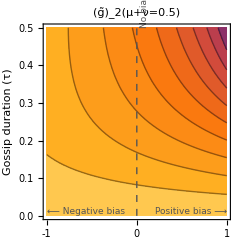
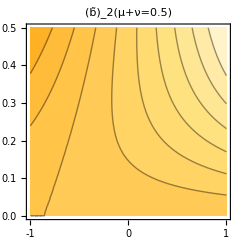
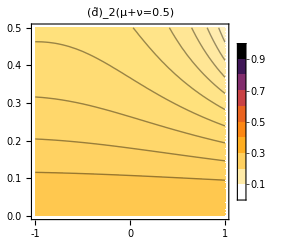
-Graphics- | -Graphics- | -Graphics-

Exported FigS5ABC.pdf to ./plots/

```mathematica
Clear[bmax,τmax,cc,uaa,uee,AAs,norm,inc];
Amax=0.5;τmax=0.5;bb=5;cc=1.;uaa=0.02;uee=0.02;norm="SJ";inc=25;
pS5ABC=plotg2b2d2[Amax,τmax,bb,cc,uaa,uee,norm,inc,False]

savefig["FigS5ABC.pdf",pS5ABC]
```

### Fig S5D–F

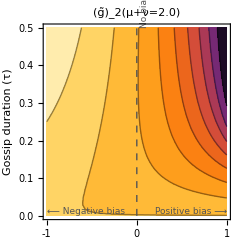
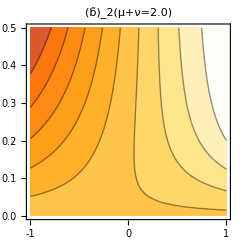
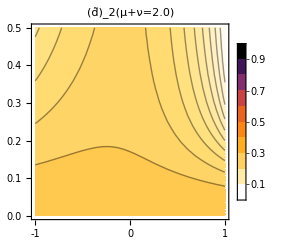
-Graphics- | -Graphics- | -Graphics-

Exported FigS5DEF.pdf to ./plots/

```mathematica
Clear[bmax,τmax,cc,uaa,uee,AAs,norm,inc];
Amax=2.0;τmax=0.5;bb=5;cc=1.;uaa=0.02;uee=0.02;norm="SJ";inc=25;
pS5DEF=plotg2b2d2[Amax,τmax,bb,cc,uaa,uee,norm,inc,False]

savefig["FigS5DEF.pdf",pS5DEF]
```

### Fig S5G–I

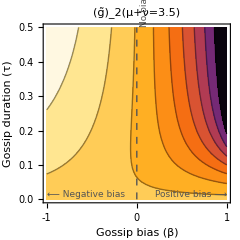
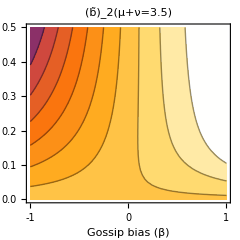
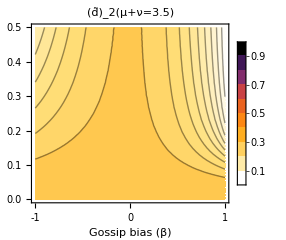
-Graphics- | -Graphics- | -Graphics-

Exported FigS5GHI.pdf to ./plots/

```mathematica
Clear[bmax,τmax,cc,uaa,uee,AAs,norm,inc];
Amax=3.5;τmax=0.5;bb=5;cc=1.;uaa=0.02;uee=0.02;norm="SJ";inc=25;
pS5GHI=plotg2b2d2[Amax,τmax,bb,cc,uaa,uee,norm,inc,False]

savefig["FigS5GHI.pdf",pS5GHI]
```

## 5.3: Stability of the DISC equilibrium against ALLD under any norm (p, q) (Figs S6)

### Functions

```mathematica
(* Fig S6 *)
plotcriticalτvβALLD[Amax_,τmax_,bb_,cc_,uaa_,uee_,norm_,inc_?NumericQ,verbose_:False]:=Module[
{p1,p2,pp,qq,col,rsol,eqns},

If[norm=="SJ",pp=0;qq=1;col=ylorrd3,
If[norm=="SS",pp=1;qq=1;col=ylorrd5,
If[norm=="SH",pp=0;qq=0;col=ylorrd1]]];

(* set norm *)
If[verbose,Print["This function is for any norm; current norm is ",norm]];
setupalleqnswithnoise[pp,qq]; (* SJ *)

(* simplify equations *)
eqns={drx==0,dry==0,drz==0}/.{δ->1};

(* solve for rx, ry, rz *)
rsol=Solve[(eqns//.eqDISC),{rx,ry,rz}];

(* check sols numerically if verbose = TRUE*)
If[verbose,
Print["Numerical example: ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}," vs ",rsol[[2]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}];
Print["The actual solution is ",rsol[[1]]/.{ua->0.02,ue->0.02,b->5,c->1,A->1.0,B->0.5,τ->1.2}]
];

(* rsol[[1]] is the actual solution *)
rsol=rsol[[1]];

p1=ListLinePlot[
Table[{BB,criticalτ2ALLD[rsol,bb,cc,uaa,uee,Amax,BB]},{BB,0.,Amax,Amax/inc}]
,Filling->Top
,PlotStyle->{Thick,col}
,PlotRange->{{0,Amax},{0.,τmax}}
,FrameLabel->{betalabel,If[((Amax==0.5)||(Amax==0.05)),τstarALLDlabel,""]}
,PlotTheme->"mk_plot"
,PlotLabel->Style["μ + ν = "<>ToString[NumberForm[Amax,{2,If[norm=="SS",2,1]}]],Black,13]
,FrameTicks->{{(({#,NumberForm[#,{2,1}],{0,0.02}})&/@Subdivide[0.,τmax,5]),None},{(({#,NumberForm[scalebias[Amax,#],{1,0},NumberPoint->""],{0,0.02}})&/@Subdivide[0,Amax,2]),None}}
,ImageSize->{280,280}
,GridLines->None
,AspectRatio->1
,Prolog->{
{Thin,Dashed,Darker[Gray],Line[{{Amax/2.,-0.1},{Amax/2.,τmax}}]}
,{AbsolutePointSize[2.5],Lighter[Gray],Point@Tuples[{Range[0,Amax,Amax/40],ConstantArray[τALLDstarplot[bb,cc,uaa,uee,pp,qq],40]}]}
}
,Epilog->{
Text[If[(Amax==0.5)||(Amax==0.05),Style["⟵ Negative bias",Darker[Gray],11],""],{0.,0.},{-1,-1}]
,Text[If[(Amax==0.5)||(Amax==0.05),Style["Positive bias ⟶",Darker[Gray],11],""],{Amax,0.},{1,-1}]
,Text[If[(Amax==0.5)||(Amax==0.05),Style["DISC stable",col,14],""],{Amax*0.99,τmax-0.01},{1,1}]
,Text[If[(Amax==0.5)||(Amax==0.05),Row[{Style["(τ^*)_ALLD",FontFamily->"Times New Roman",Gray,11]
,Style[" without noise",FontFamily->"Arial",Gray,10]}
,BaselinePosition->Center]],{0.,(τALLDstarplot[bb,cc,uaa,uee,pp,qq])},{-1,1}]
}
];
Show@p1
]
```

### Fig S6A–C

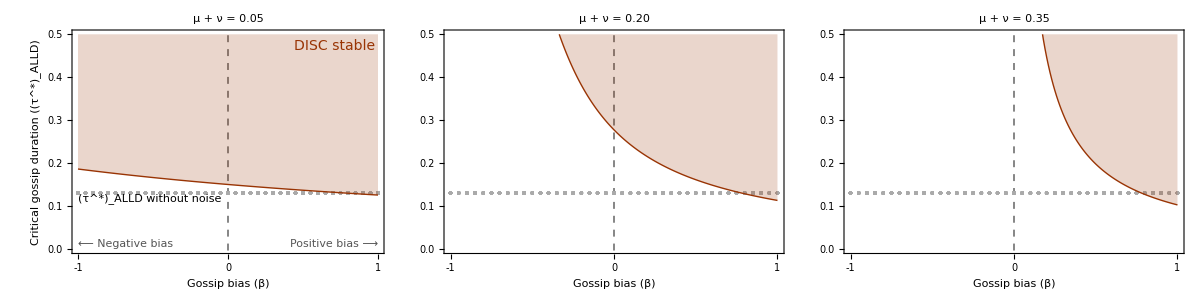

Exported FigS6ABC.pdf to ./plots/

```mathematica
Clear[Amax,τmax];τmax=0.5;bb=1.2;cc=1.;uaa=0.02;uee=0.02;norm="SS";inc=200;
pS6ABC=Grid[{plotcriticalτvβALLD[#,τmax,bb,cc,uaa,uee,norm,inc,False]&/@{0.5/10,2./10,3.5/10}},Spacings->0.0]

savefig["FigS6ABC.pdf",pS6ABC]
```

### Fig S6D–F

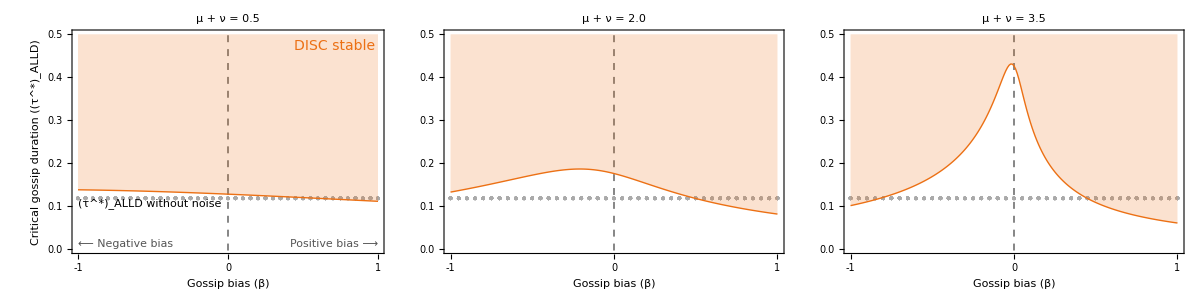

Exported FigS6DEF.pdf to ./plots/

```mathematica
Clear[Amax,τmax];τmax=0.5;bb=5;cc=1.;uaa=0.02;uee=0.02;norm="SJ";inc=200;
pS6DEF=Grid[{plotcriticalτvβALLD[#,τmax,bb,cc,uaa,uee,norm,inc,False]&/@({0.5,2.,3.5})},Spacings->0.0]

savefig["FigS6DEF.pdf",pS6DEF]
```

### Fig S6G–I

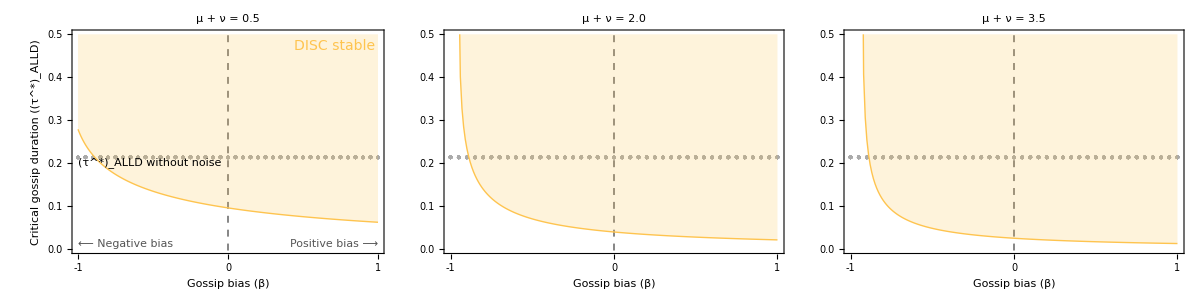

Exported FigS6GHI.pdf to ./plots/

```mathematica
Clear[Amax,τmax];τmax=0.5;bb=5.;cc=1.;uaa=0.02;uee=0.02;norm="SH";inc=200;
pS6GHI=Grid[{plotcriticalτvβALLD[#,τmax,bb,cc,uaa,uee,norm,inc,False]&/@({0.5,2.,3.5})},Spacings->0.0]

savefig["FigS6GHI.pdf",pS6GHI]
```